This notebook will guide you through the process of generating WT and tumor SH2-phosphoprotein networks from MSM predictions.

Manually set root directory (where repository contents were unpacked) to fldr symbol.

```mathematica
fldr="/sh2-cancer/";(* Set to correct folder where repository contents were unpacked. *)
"Done"
```

Done

Set other directories

```mathematica
fldrData=FileNameJoin[{fldr,"data"}];
fldrCode=FileNameJoin[{fldr,"code"}];
"Done"
```

Done

Load Mathematica packages

```mathematica
Get[FileNameJoin[{fldrCode,#}]]&/@{"misc.wl","visualization.wl"};
"Loaded"
```

Loaded

Load needed symbols. They are:
matProbProteinInteractHumanWTFilteredByRef2FirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15: MSM/P predictions of SH2-phosphoprotein network.
matTypelessSystemAndModelPosteriorProteinInteractTumorMutantsVer3FilteredByRef2AndHTFirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15: MSM/N predictions of general tumor network, broken by mutation type.
matSystemAndModelPosteriorProteinInteractTumorMutantsVer3FilteredByRef2AndHTFirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15: MSM/N predictions of general tumor network.
matsTypelessSystemAndModelPosteriorProteinInteractTumorSpecificMutantsVer3FilteredByRef2AndHTFirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15: MSM/N predictions of all tissue-specific tumor networks, broken by mutation type.
matsSystemAndModelPosteriorProteinInteractTumorSpecificMutantsVer3FilteredByRef2AndHTFirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15: MSM/N predictions of all tissue-specific tumor networks.
metadataWithIdxGrpByGeneSH2DomainsHumanVer3: Metadata for all SH2 domain-containing proteins in the human genome.
metadataWithIdxGrpByGenePhosphositesHumanVer3: Metadata for all phosphoproteins in the human genome.
metadataAugmentedWithIdxSH2DomainsTumorMutantsVer3: Metadata for all SH2 domain mutations in COSMIC.
metadataAugmentedWithIdxPhosphositesTumorMutantsVer3: Metadata for all phosphoprotein mutations in COSMIC.
lblsTumorTypesFSORNCNDPFBASCPC: Labels for all tumor types.
metadataOncogenes: List of known oncogenes
metadataTumorSuppressors: Lost of known tumor suppressors

```mathematica
LoadSymbol[fldrData,
{matProbProteinInteractHumanWTFilteredByRef2FirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15,
matTypelessSystemAndModelPosteriorProteinInteractTumorMutantsVer3FilteredByRef2AndHTFirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15,
matSystemAndModelPosteriorProteinInteractTumorMutantsVer3FilteredByRef2AndHTFirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15,
matsTypelessSystemAndModelPosteriorProteinInteractTumorSpecificMutantsVer3FilteredByRef2AndHTFirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15,
matsSystemAndModelPosteriorProteinInteractTumorSpecificMutantsVer3FilteredByRef2AndHTFirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15,
metadataWithIdxGrpByGeneSH2DomainsHumanVer3,
metadataWithIdxGrpByGenePhosphositesHumanVer3,
metadataAugmentedWithIdxSH2DomainsTumorMutantsVer3,
metadataAugmentedWithIdxPhosphositesTumorMutantsVer3,
lblsTumorTypesFSORNCNDPFBASCPC,
metadataOncogenes,
metadataTumorSuppressors}]
```

Loaded

Generate adjacency matrix from MSM/P predictions.

```mathematica
adjmatProbProteinInteractHumanWTFilteredByRef2FirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15=Block[
{datSH2=metadataWithIdxGrpByGeneSH2DomainsHumanVer3,datPhosphosites=DeleteCases[DeleteCases[metadataWithIdxGrpByGenePhosphositesHumanVer3,{_,_,_,_,_,0|1,_},{2}],{}],mat=matProbProteinInteractHumanWTFilteredByRef2FirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15,mapSH2,mapPhosphosites,labels},
labels=Union[datSH2⟦All,1,2⟧,datPhosphosites⟦All,1,2⟧];
{mapSH2,mapPhosphosites}=Map[Position[labels,#]⟦1,1⟧&,{datSH2⟦All,1,2⟧,datPhosphosites⟦All,1,2⟧},{2}];
SparseArray[Flatten[Outer[List,mapSH2,mapPhosphosites],1]->Flatten[mat],{Length[labels],Length[labels]}]];
GenerateSymbol[fldrData,adjmatProbProteinInteractHumanWTFilteredByRef2FirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15];
"Done"
```

Done

Visualize WT SH2-phosphoprotein network using a cutoff probability of interaction of P=0.85.

```mathematica
With[{cutoff=0.85,blue=RGBColor[0/255,126/255,234/255],red=RGBColor[234/255,21/255,122/255]},Block[
{mat=adjmatProbProteinInteractHumanWTFilteredByRef2FirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15,datSH2=metadataWithIdxGrpByGeneSH2DomainsHumanVer3,datPhosphosites=DeleteCases[DeleteCases[metadataWithIdxGrpByGenePhosphositesHumanVer3,{_,_,_,_,_,0|1,_},{2}],{}],labelsOncogenes=metadataOncogenes,labelsTS=metadataTumorSuppressors,matBinary,singletons,labelsSH2,labelsPeptide,labelsEither,styleVertices,graph,shapeVertices,flags},
{labelsSH2,labelsPeptide}=#⟦All,1,2⟧&/@{datSH2,datPhosphosites};
labelsEither=Union[labelsSH2,labelsPeptide];
flags=Table[MemberQ[labels,#],{labels,{labelsSH2,labelsPeptide,labelsOncogenes,labelsTS}}]&/@labelsEither;
shapeVertices=MapIndexed[Function[{flagset,pos},pos⟦1⟧->(Inset[Graphics[{Blend[{red,blue},flagset⟦;;2⟧/.{{True,False}->0,{False,True}->1,{True,True}->0.5}],Disk[{0,0},1],White,Thick,If[flagset⟦3⟧,Line[{{-0.5,0},{0.5,0}}]],If[flagset⟦4⟧,Line[{{0,-0.5},{0,0.5}}]]}],#,Automatic,0.1]&)],flags];
matBinary=Ceiling[Chop[mat,cutoff]];
singletons=Flatten[Position[Table[Total[{matBinary⟦i,;;⟧,matBinary⟦;;,i⟧},∞]===0,{i,Length[matBinary]}],True]];
graph=AdjacencyGraph[matBinary,VertexShapeFunction->shapeVertices,BaseStyle->EdgeForm[None],EdgeStyle->Directive[Opacity[0.5],Gray],EdgeShapeFunction->GraphElementData[{"FilledArrow","ArrowSize"->.012}],VertexLabels->Thread[Range[Length[labelsEither]]->labelsEither],VertexLabelStyle->Directive[FontFamily->"Arial",GrayLevel[0.3],FontSize->11]];
Show[VertexDelete[graph,singletons],ImageSize->1200]]]
```

-Graphics-

High-level overviews of the network at different probability thresholds:

```mathematica
Table[Block[
{weighted=False,mat=adjmatProbProteinInteractHumanWTFilteredByRef2FirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15,datSH2=metadataWithIdxGrpByGeneSH2DomainsHumanVer3,datPhosphosites=DeleteCases[DeleteCases[metadataWithIdxGrpByGenePhosphositesHumanVer3,{_,_,_,_,_,0|1,_},{2}],{}],blue=RGBColor[0/255,126/255,234/255],red=RGBColor[234/255,21/255,122/255],matBinary,singletons,labelsSH2,labelsPeptide,labelsBoth,labelsEither,idxesSH2,idxesPeptide,idxesBoth,styleVertices,graph},
{labelsSH2,labelsPeptide}=#⟦All,1,2⟧&/@{datSH2,datPhosphosites};
labelsBoth=Intersection[labelsSH2,labelsPeptide];
labelsEither=Union[labelsSH2,labelsPeptide];
{idxesSH2,idxesPeptide,idxesBoth}=Map[Position[labelsEither,#]⟦1,1⟧&,{labelsSH2,labelsPeptide,labelsBoth},{2}];
styleVertices=Flatten[MapThread[Thread[#1->ConstantArray[#2,Length[#1]]]&,{{idxesSH2,idxesPeptide,idxesBoth},{red,blue,Blend[{red,blue},0.5]}}]];
matBinary=Chop[mat,cutoff];
singletons=Flatten[Position[Table[Total[{matBinary⟦i,;;⟧,matBinary⟦;;,i⟧},∞]===0,{i,Length[matBinary]}],True]];
graph=WeightedAdjacencyGraph[-Log[matBinary],VertexStyle->styleVertices,VertexSize->0.6,BaseStyle->EdgeForm[None],EdgeStyle->Directive[Opacity[0.3],Gray],EdgeShapeFunction->GraphElementData[{"FilledArrow","ArrowSize"->.01}],VertexLabelStyle->Directive[FontFamily->"Calibri",GrayLevel[0.3],FontSize->12],GraphLayout->{"SpringElectricalEmbedding","EdgeWeighted"->weighted,"RepulsiveForcePower"->-1}];
Show[VertexDelete[graph,singletons]]],{cutoff,0.99,0.80,-0.01}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Generate adjacency matrix from MSM/N predictions for the general tumor network.

```mathematica
adjmatTypelessSystemAndModelPosteriorProteinInteractTumorMutantsVer3FilteredByRef2AndHTFirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15=Block[
{datSH2=metadataWithIdxGrpByGeneSH2DomainsHumanVer3,datPhosphosites=DeleteCases[DeleteCases[metadataWithIdxGrpByGenePhosphositesHumanVer3,{_,_,_,_,_,0|1,_},{2}],{}],mat=matTypelessSystemAndModelPosteriorProteinInteractTumorMutantsVer3FilteredByRef2AndHTFirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15,mapSH2,mapPhosphosites,labels},
labels=Union[datSH2⟦All,1,2⟧,datPhosphosites⟦All,1,2⟧];
{mapSH2,mapPhosphosites}=Map[Position[labels,#]⟦1,1⟧&,{datSH2⟦All,1,2⟧,datPhosphosites⟦All,1,2⟧},{2}];
SparseArray[Flatten[Outer[List,mapSH2,mapPhosphosites],1]->Normal[Flatten[mat]],{Length[labels],Length[labels]}]];
adjmatMaxTypeSystemAndModelPosteriorProteinInteractTumorMutantsVer3FilteredByRef2AndHTFirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15=Block[
{datSH2=metadataWithIdxGrpByGeneSH2DomainsHumanVer3,datPhosphosites=DeleteCases[DeleteCases[metadataWithIdxGrpByGenePhosphositesHumanVer3,{_,_,_,_,_,0|1,_},{2}],{}],mat=matSystemAndModelPosteriorProteinInteractTumorMutantsVer3FilteredByRef2AndHTFirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15,mapSH2,mapPhosphosites,labels},
labels=Union[datSH2⟦All,1,2⟧,datPhosphosites⟦All,1,2⟧];
{mapSH2,mapPhosphosites}=Map[Position[labels,#]⟦1,1⟧&,{datSH2⟦All,1,2⟧,datPhosphosites⟦All,1,2⟧},{2}];
SparseArray[Flatten[Outer[List,mapSH2,mapPhosphosites],1]->Flatten[Map[MaxPosition,Normal[mat],{2}]],{Length[labels],Length[labels]}]];
GenerateSymbol[fldrData,{adjmatTypelessSystemAndModelPosteriorProteinInteractTumorMutantsVer3FilteredByRef2AndHTFirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15,
adjmatMaxTypeSystemAndModelPosteriorProteinInteractTumorMutantsVer3FilteredByRef2AndHTFirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15}];
"Done"
```

Done

Visualize general SH2-phosphoprotein tumor network using a cutoff probability of interaction of P_perturb=0.0015 . Three outliers are removed (PTPN11, PTEN, and FRK).

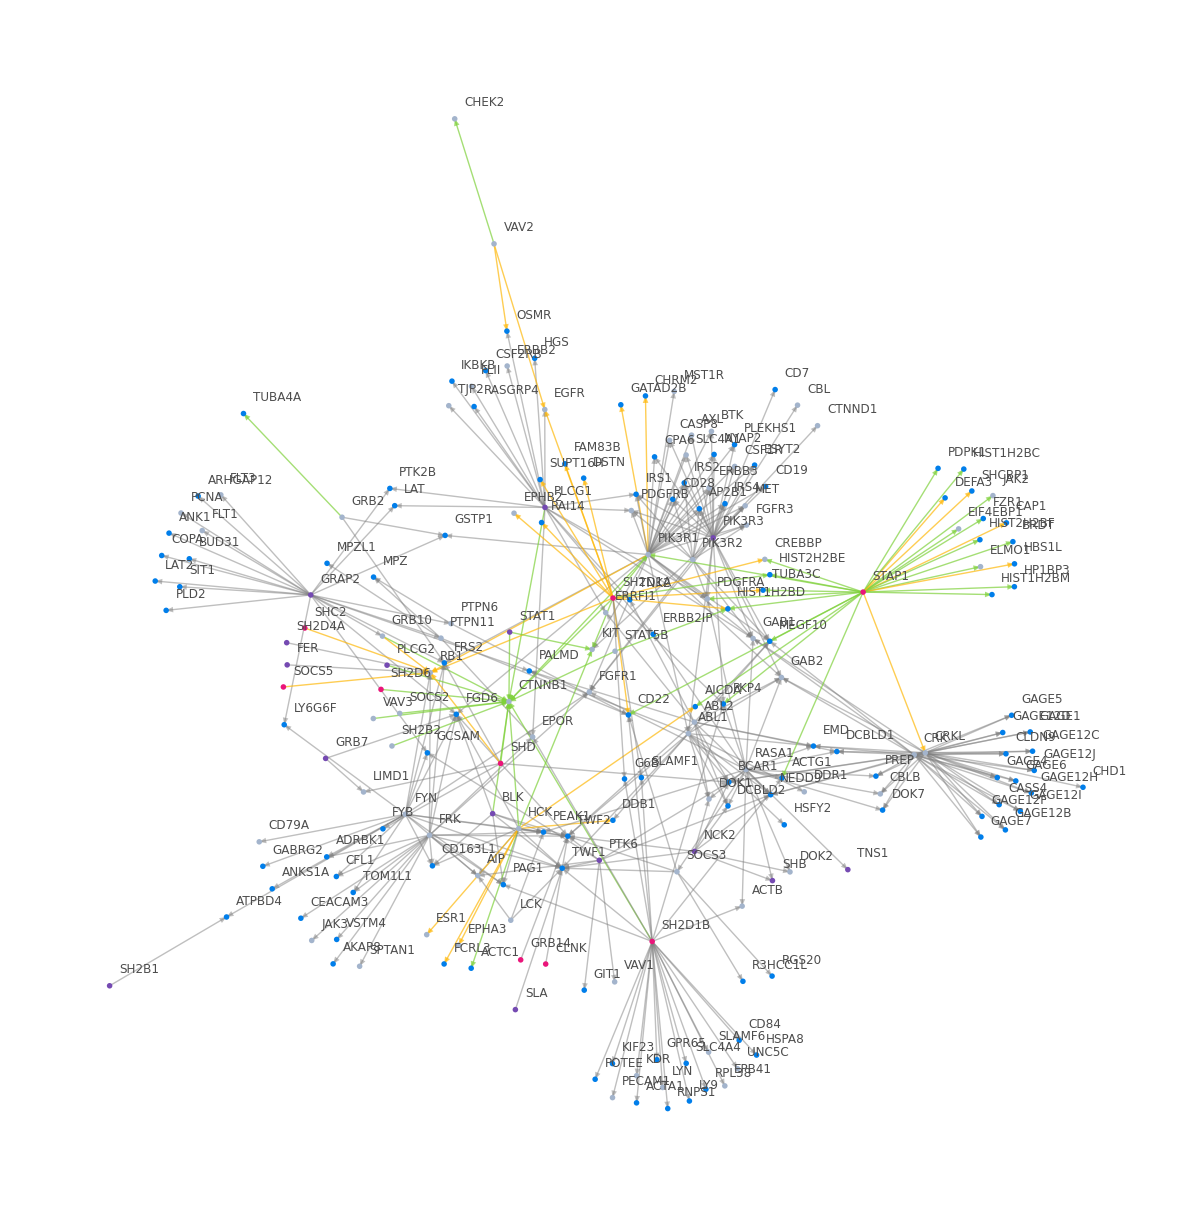

```mathematica
With[{outliers={"PTPN11","PTEN","FRK"},cutoff1=0.85,cutoff2=0.0015,
blue=RGBColor[0/255,126/255,234/255],red=RGBColor[234/255,21/255,122/255],green=RGBColor[127/255,209/255,59/255],orange=RGBColor[254/255,184/255,10/255]},Block[
{mat1=adjmatProbProteinInteractHumanWTFilteredByRef2FirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15,mat2=adjmatTypelessSystemAndModelPosteriorProteinInteractTumorMutantsVer3FilteredByRef2AndHTFirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15,mat3=adjmatMaxTypeSystemAndModelPosteriorProteinInteractTumorMutantsVer3FilteredByRef2AndHTFirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15,datSH2=metadataWithIdxGrpByGeneSH2DomainsHumanVer3,datPhosphosites=DeleteCases[DeleteCases[metadataWithIdxGrpByGenePhosphositesHumanVer3,{_,_,_,_,_,0|1,_},{2}],{}],labelsOncogenes=metadataOncogenes030414,labelsTS=metadataTumorSuppressors,matBinary1,matBinary2,singletons1,singletons2,labelsSH2,labelsPeptide,flags,labelsEither,shapeVertices,graph1,graph2,el1,el2,colorsTypes},
{labelsSH2,labelsPeptide}=#⟦All,1,2⟧&/@{datSH2,datPhosphosites};
labelsEither=Union[labelsSH2,labelsPeptide];
flags=Table[MemberQ[labels,#],{labels,{labelsSH2,labelsPeptide,labelsOncogenes,labelsTS}}]&/@labelsEither;
shapeVertices=MapIndexed[Function[{flagset,pos},pos⟦1⟧->(Inset[Graphics[{Blend[{red,blue},flagset⟦;;2⟧/.{{True,False}->0,{False,True}->1,{True,True}->0.5}],Disk[{0,0},1],White,Thick,If[flagset⟦3⟧,Line[{{-0.5,0},{0.5,0}}]],If[flagset⟦4⟧,Line[{{0,-0.5},{0,0.5}}]]}],#,Automatic,0.1]&)],flags];
matBinary1=Ceiling[Chop[mat1,cutoff1]];
matBinary2=Ceiling[Chop[mat2,cutoff2]];
matBinary2=ReplacePart[matBinary2,Position[labelsEither,Alternatives@@outliers]->ConstantArray[0,Dimensions[matBinary2]⟦2⟧]];
matBinary2=Transpose[ReplacePart[Transpose[matBinary2],Position[labelsEither,Alternatives@@outliers]->ConstantArray[0,Dimensions[matBinary2]⟦1⟧]]];
singletons1=Flatten[Position[Table[Total[{matBinary1⟦i,;;⟧,matBinary1⟦;;,i⟧},∞]===0,{i,Length[matBinary1]}],True]];
singletons2=Flatten[Position[Table[Total[{matBinary2⟦i,;;⟧,matBinary2⟦;;,i⟧},∞]===0,{i,Length[matBinary2]}],True]];
graph1=AdjacencyGraph[matBinary1];
graph2=AdjacencyGraph[matBinary2];
el1=EdgeList[graph1];
el2=EdgeList[graph2];
colorsTypes=Extract[mat3,Transpose[{el2⟦All,1⟧,el2⟦All,2⟧}]]/.{1->Directive[green],2->Directive[orange]};
Show[VertexDelete[GraphUnion[graph1,graph2,VertexShapeFunction->shapeVertices,BaseStyle->EdgeForm[None],EdgeShapeFunction->GraphElementData[{"FilledArrow","ArrowSize"->.012}],VertexLabels->Thread[Range[Length[labelsEither]]->labelsEither],VertexLabelStyle->Directive[FontFamily->"Calibri",GrayLevel[0.3],FontSize->12],EdgeStyle->Join[Thread[el2->colorsTypes],Thread[Complement[el1,el2]->Directive[Opacity[0.5],Gray]]]],Intersection[singletons1,singletons2]],ImageSize->1200]]]
```

Generate adjacency matrices from MSM/N predictions for the tumor tissue types.

```mathematica
adjmatsTypelessSystemAndModelPosteriorProteinInteractTumorSpecificMutantsVer3FilteredByRef2AndHTFSORNCNDPFBASCPCDist15=Block[
{datSH2=metadataWithIdxGrpByGeneSH2DomainsHumanVer3,datPhosphosites=DeleteCases[DeleteCases[metadataWithIdxGrpByGenePhosphositesHumanVer3,{_,_,_,_,_,0|1,_},{2}],{}],mats=matsTypelessSystemAndModelPosteriorProteinInteractTumorSpecificMutantsVer3FilteredByRef2AndHTFirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15,mapSH2,mapPhosphosites,labels},
labels=Union[datSH2⟦All,1,2⟧,datPhosphosites⟦All,1,2⟧];
{mapSH2,mapPhosphosites}=Map[Position[labels,#]⟦1,1⟧&,{datSH2⟦All,1,2⟧,datPhosphosites⟦All,1,2⟧},{2}];
SparseArray[Flatten[Outer[List,mapSH2,mapPhosphosites],1]->Normal[Flatten[#]],{Length[labels],Length[labels]}]&/@mats];
adjmatsMaxTypeSystemAndModelPosteriorProteinInteractTumorSpecificMutantsVer3FilteredByRef2AndHTFSORNCNDPFBASCPCDist15=Block[
{datSH2=metadataWithIdxGrpByGeneSH2DomainsHumanVer3,datPhosphosites=DeleteCases[DeleteCases[metadataWithIdxGrpByGenePhosphositesHumanVer3,{_,_,_,_,_,0|1,_},{2}],{}],mats=matsSystemAndModelPosteriorProteinInteractTumorSpecificMutantsVer3FilteredByRef2AndHTFirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15,mapSH2,mapPhosphosites,labels},
labels=Union[datSH2⟦All,1,2⟧,datPhosphosites⟦All,1,2⟧];
{mapSH2,mapPhosphosites}=Map[Position[labels,#]⟦1,1⟧&,{datSH2⟦All,1,2⟧,datPhosphosites⟦All,1,2⟧},{2}];
SparseArray[Flatten[Outer[List,mapSH2,mapPhosphosites],1]->Flatten[Map[MaxPosition,Normal[#],{2}]],{Length[labels],Length[labels]}]&/@mats];
GenerateSymbol[fldrData,
{adjmatsTypelessSystemAndModelPosteriorProteinInteractTumorSpecificMutantsVer3FilteredByRef2AndHTFSORNCNDPFBASCPCDist15,
adjmatsMaxTypeSystemAndModelPosteriorProteinInteractTumorSpecificMutantsVer3FilteredByRef2AndHTFSORNCNDPFBASCPCDist15}];
"Done"
```

Done

Visualize all tissue-specific tumor networks (showing top 20 perturbed edges):

```mathematica
With[{nEdges=20,cutoff1=0.85,mats2=adjmatsTypelessSystemAndModelPosteriorProteinInteractTumorSpecificMutantsVer3FilteredByRef2AndHTFSORNCNDPFBASCPCDist15,mats3=adjmatsMaxTypeSystemAndModelPosteriorProteinInteractTumorSpecificMutantsVer3FilteredByRef2AndHTFSORNCNDPFBASCPCDist15,lbls=lblsTumorTypesFSORNCNDPFBASCPC,blue=RGBColor[0/255,126/255,234/255],red=RGBColor[234/255,21/255,122/255],green=RGBColor[127/255,209/255,59/255],orange=RGBColor[254/255,184/255,10/255]},
MapThread[
Block[
{cutoff2=Reverse[Sort[Normal[Flatten[#1]]]]⟦nEdges⟧,mat1=adjmatProbProteinInteractHumanWTFilteredByRef2FirstAndSecondOrderResiduesNoCNoDashPositionsFilteredByAvgStructuralCPCutoffsDist15,mat2=#1,mat3=#2,datSH2=metadataWithIdxGrpByGeneSH2DomainsHumanVer3,datPhosphosites=DeleteCases[DeleteCases[metadataWithIdxGrpByGenePhosphositesHumanVer3,{_,_,_,_,_,0|1,_},{2}],{}],labelsOncogenes=metadataOncogenes030414,labelsTS=metadataTumorSuppressors,matBinary1,matBinary2,singletons1,singletons2,labelsSH2,labelsPeptide,flags,labelsEither,shapeVertices,graph1,graph2,el1,el2,colorsTypes},
{labelsSH2,labelsPeptide}=#⟦All,1,2⟧&/@{datSH2,datPhosphosites};
labelsEither=Union[labelsSH2,labelsPeptide];
flags=Table[MemberQ[labels,#],{labels,{labelsSH2,labelsPeptide,labelsOncogenes,labelsTS}}]&/@labelsEither;
shapeVertices=MapIndexed[Function[{flagset,pos},pos⟦1⟧->(Inset[Graphics[{Blend[{red,blue},flagset⟦;;2⟧/.{{True,False}->0,{False,True}->1,{True,True}->0.5}],Disk[{0,0},1],White,Thick,If[flagset⟦3⟧,Line[{{-0.5,0},{0.5,0}}]],If[flagset⟦4⟧,Line[{{0,-0.5},{0,0.5}}]]}],#,Automatic,0.1]&)],flags];
matBinary1=Ceiling[Chop[mat1,cutoff1]];
matBinary2=Ceiling[Chop[mat2,cutoff2]];
singletons1=Flatten[Position[Table[Total[{matBinary1⟦i,;;⟧,matBinary1⟦;;,i⟧},∞]===0,{i,Length[matBinary1]}],True]];
singletons2=Flatten[Position[Table[Total[{matBinary2⟦i,;;⟧,matBinary2⟦;;,i⟧},∞]===0,{i,Length[matBinary2]}],True]];
graph1=AdjacencyGraph[matBinary1];
graph2=AdjacencyGraph[matBinary2];
el1=EdgeList[graph1];
el2=EdgeList[graph2];
colorsTypes=Extract[mat3,Transpose[{el2⟦All,1⟧,el2⟦All,2⟧}]]/.{1->Directive[Thickness[0.0016],green],2->Directive[Thickness[0.0016],orange]};
Show[VertexDelete[GraphUnion[graph1,graph2,VertexShapeFunction->shapeVertices,BaseStyle->EdgeForm[None],EdgeShapeFunction->GraphElementData[{"FilledArrow","ArrowSize"->.012}],VertexLabels->Thread[Range[Length[labelsEither]]->labelsEither],VertexLabelStyle->Directive[FontFamily->"Calibri",GrayLevel[0.3],FontSize->12],EdgeStyle->Join[Thread[el2->colorsTypes],Thread[Complement[el1,el2]->Directive[Opacity[0.5],Gray]]]],Intersection[singletons1,singletons2]],ImageSize->1000,PlotLabel->#3]]&,
{mats2,mats3,lbls}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}